# Life-Cycle Problems: Arbitrary Numbers of Periods

```mathematica
x=0; Remove["Global`*"];DateList[Date[]]//Most
```

{2020,3,9,21,27}

## Life-Cycle Consumption with longer life

### Setup

Let Cons[t] be consumption in period t, where "life" begins at t=1 and continues to t=T. We assume that the utility at time t is u[Cons[t]] and that utility is discounted at β. Therefore, the life-cycle objective is

```mathematica
obj := Sum[β^(t-1) u[Subscript[Cons, t]],{t,1,T}]
```

R will be the discount factor, which is also one plus the interest rate; hence, a dollar saved at time t will be worth R=1+r at time t+1. Let wage[t] be the labor income in period t.
The present values of consumption expenditures and wage income are

```mathematica
PVc:= Sum[Subscript[Cons, t] R^(-t+1),{t,1,T}] 
PVw:= Sum[Subscript[wage, t] R^(-t+1),{t,1,T}]
```

The budget constraint implies that present value of consumption equals (or, is less than) the present value of wage income.

```mathematica
Budget:={PVc≤ PVw}
```

List the variables

```mathematica
vars:=Table[Subscript[Cons, t],{t,1,T}]
```

Add lower bound constraints on consumption.

```mathematica
LoBnds:=Table[Subscript[Cons, t]≥ 0.0001,{t,1,T}]
```

Now we form a new constraint set combining the budget constraint with the positivity constraints.

```mathematica
constraints:=Union[Budget,LoBnds]
```

### First examples

#### Exponential utility

Choose the utility function and discount factor.

```mathematica
u[c_] = -Exp[-c]; β=0.96;
```

Choose the interest rate.

```mathematica
r=0.10;R=1 + r;
```

Choose the planning horizon.

```mathematica
T=4;
```

Specify the income path. We choose a pattern that corresponds to a common (parabolic) pattern of life-cycle earnings,

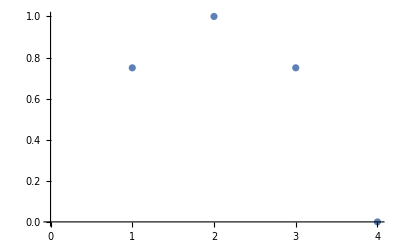

```mathematica
Do[Subscript[wage, i]=(T-i)i/T,{i,1,T}]
Table[Subscript[wage, i],{i,1,T}];
ListPlot[%]
```

Display the variables, objective, and constraints:

```mathematica
vars
```

{Cons_1,Cons_2,Cons_3,Cons_4}

```mathematica
obj
```

-1. ⅇ^-Cons_1-0.96 ⅇ^-Cons_2-0.9216 ⅇ^-Cons_3-0.884736 ⅇ^-Cons_4

```mathematica
constraints//TableForm
```

Cons_1≥0.0001
Cons_2≥0.0001
Cons_3≥0.0001
Cons_4≥0.0001
1. Cons_1+0.909091 Cons_2+0.826446 Cons_3+0.751315 Cons_4≤2.27893

Call the optimizer

```mathematica
sol=FindMaximum[{obj,constraints},vars]
```

{-1.95557,{Cons_1→0.578319,Cons_2→0.632808,Cons_3→0.687296,Cons_4→0.741784}}

Extract the consumption path solution and plot it:

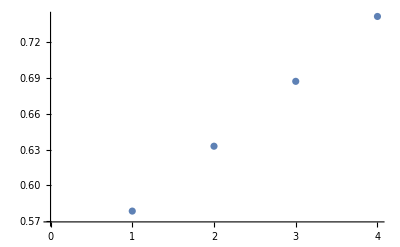

```mathematica
Table[Subscript[Cons, i],{i,1,T}]/.sol[[2]]
ListPlot[%]
```

#### Square root utility

Change the utility function.

```mathematica
u[c_] = Sqrt[c];
```

Call the optimizer

```mathematica
sol=FindMaximum[{obj,constraints},vars]
```

{3.05051,{Cons_1→0.558106,Cons_2→0.622364,Cons_3→0.694021,Cons_4→0.773927}}

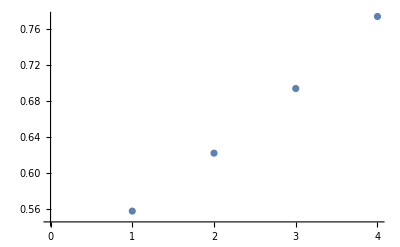

```mathematica
Table[Subscript[Cons, i],{i,1,T}]/.sol[[2]];
ListPlot[%]
```

#### -c^-3 utility, longer horizon

Change the utility function and horizon, adjusting wage rates accordingly.

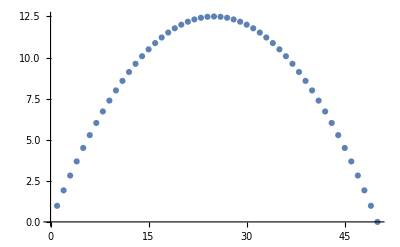

```mathematica
T=50;
Do[Subscript[wage, i]=(T-i)i/T,{i,1,T}]
Table[Subscript[wage, i],{i,1,T}];
ListPlot[%]
```

```mathematica
u[c_] = -c^-3;
```

Call the optimizer

```mathematica
sol=FindMaximum[{obj,constraints},vars];
```

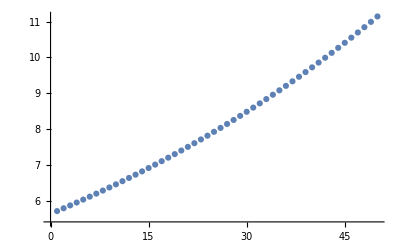

```mathematica
Table[Subscript[Cons, i],{i,1,T}]/.sol[[2]];
ListPlot[%]
```

#### T=250, quarterly calibration

Set T to be 250 and treat time period as a quarter

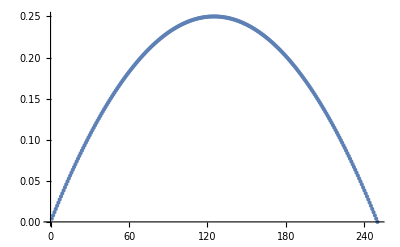

```mathematica
T=250;
Do[Subscript[wage, i]=(T-i)i/T^2,{i,1,T}]
Table[Subscript[wage, i],{i,1,T}]//ListPlot
```

Choose an interest rate and a discount factor

```mathematica
r=0.01;R=1 + r; β=0.991;
```

Specify a utility function

```mathematica
u[c_] = -Exp[-c];
```

Solve and plot the solution

```mathematica
sol=FindMaximum[{obj,constraints},vars];//Timing
```

{0.825668,Null}

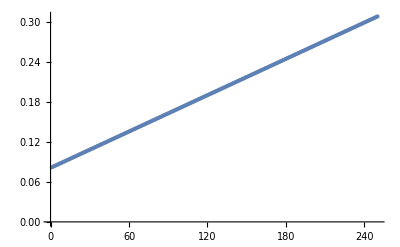

```mathematica
ListPlot[vars/.sol[[2]]]
```

## Life-Cycle Consumption with long life - examples of algorithm failure

```mathematica
x=0; Remove["Global`*"]
```

### Setup

```mathematica
obj := Sum[β^(t-1) u[Cons[t]],{t,1,T}]
PVc:= Sum[Cons[t] R^(-t+1),{t,1,T}] 
PVw:= Sum[wage[t] R^(-t+1),{t,1,T}] 
Budget:={PVc≤ PVw}
LoBnds:=Table[Cons[t]≥ 0.0001,{t,1,T}]
constraints:=Union[Budget,LoBnds]
vars:=Table[Cons[t],{t,1,T}]
```

### Examples of failure

#### Exponential utility

Choose the utility function and discount factor.

```mathematica
u[c_] = -Exp[-c]; β=0.9;
```

Choose the interest rate and planning horizon.

```mathematica
r=0.15;R=1 + r; T=250;
```

Specify the income path. We choose a pattern that corresponds to a common (parabolic) pattern of life-cycle earnings,

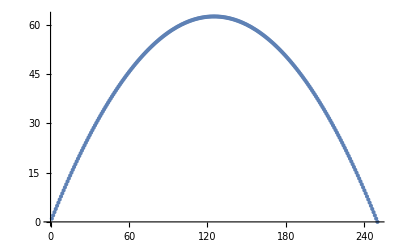

```mathematica
Do[wage[i]=(T-i)i/T,{i,1,T}]
ListPlot[Table[wage[i],{i,1,T}]]
```

Call the optimizer, extract the consumption path solution, and plot it

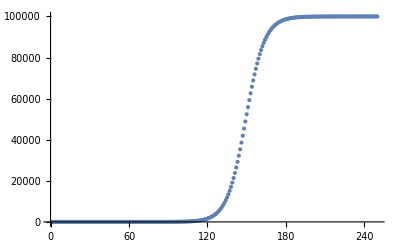

```mathematica
sol=FindMaximum[{obj,constraints},vars];
csol=Table[Cons[i],{i,1,T}]/.sol[[2]];ListPlot[csol]
```

```mathematica
β^T
```

3.63603×10^-12

#### Square root utility

Change the utility function.

```mathematica
u[c_] = Sqrt[c];
```

Call the optimizer, and plot the solution

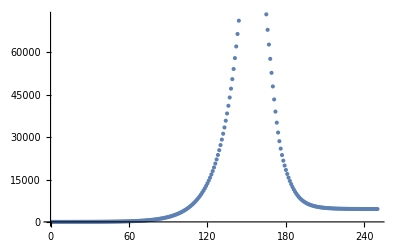

```mathematica
sol=FindMaximum[{obj,constraints},vars];
csol=Table[Cons[i],{i,1,T}]/.sol[[2]]; ListPlot[csol]
```

## Life-Cycle Consumption with long life - how to fix the failures

```mathematica
x=0; Remove["Global`*"]
```

#### Setup

```mathematica
obj := Sum[β^t u[Cons[t]],{t,1,T}]
vars:=Table[Cons[t],{t,1,T}]
PVc:= Sum[Cons[t] R^(-t+1),{t,1,T}] 
PVw:= Sum[wage[t] R^(-t+1),{t,1,T}] 
Budget:={PVc≤ PVw}
LoBnds:=Table[Cons[t]≥ 0.0001,{t,1,T}]
```

Here is the new step: express the Euler equations, one for each time t:

```mathematica
euler:=Table[u'[Cons[t]]==β R u'[Cons[t+1]],{t,1,T-1}]
```

We add the list euler to the constraints:

```mathematica
constraints:=Union[Budget,LoBnds,euler]
```

This problem has T unknown consumptions and T equality constraints: the budget constraint and T-1 Euler equations. So, the number of shadow prices equals for the equality constraints the number of unknowns. As long as there are no active lower bound constraints (which there should not be), there is a good chance that LICQ will hold.

#### Exponential utility

```mathematica
u[c_] = -Exp[-c]; β=0.9;
r=0.15;R=1 + r; T=150;
β^T
```

1.36891×10^-7

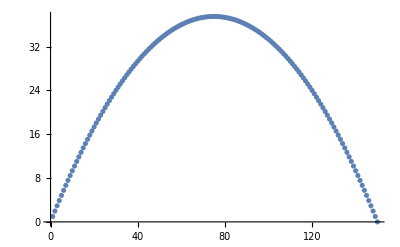

```mathematica
Do[wage[i]=(T-i)i/T,{i,1,T}]
tab=Table[wage[i],{i,1,T}]; ListPlot[tab]
```

Call the optimizer

{0.84729,Null}

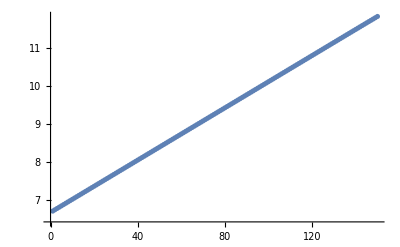

```mathematica
sol=FindMaximum[{obj,constraints},vars];//Timing
csol=Table[Cons[i],{i,1,T}]/.sol[[2]]; ListPlot[csol]
```

This now works. The Euler equation constraints have pushed the solver to find the true solution.

#### Make objective degenerate

The approach of adding first-order conditions to the problem is a bit strange. It is better to keep the Euler equations and get rid of the objective function.

```mathematica
obj=1;
sol=FindMaximum[{obj,constraints},vars];//Timing
```

{12.9876,Null}

Extract and plot the consumption path solution

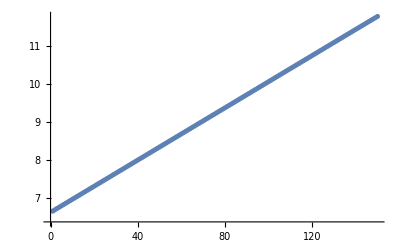

```mathematica
csol=Table[Cons[i],{i,1,T}]/.sol[[2]]; ListPlot[csol]
```

#### Square root utility

Even when we add the Euler equations, other things may go wrong.

```mathematica
T=150;
```

```mathematica
u[c_] = Sqrt[c];
```

```mathematica
euler:=Table[u'[Cons[t]]==β R u'[Cons[t+1]],{t,1,T-1}]
```

```mathematica
sol=FindMaximum[{obj,constraints},vars];//Timing
```

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {49.2337, 1.38494, 2.92027}, is returned.

{111.61,Null}

Convergence was slow. The iteration limit was 500, and the result was not good.

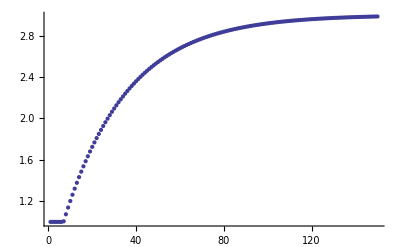

```mathematica
csol=Table[Cons[i],{i,1,T}]/.sol[[2]]; ListPlot[csol]
```

NOTE: The sol=... and Table... commands have been disabled. The most recent version of Mathematica successfully solves this problem.

#### A fix for the square root utility failure

Change the Euler equation constraint by nonlinear transformation.

If u[c] is the square root function, then the inverse of the u'[c] function is 1/(4 u'[c]^2)

```mathematica
u[c_] = Sqrt[c];
upinv[up_]=1/(4 up^2);
```

Apply (u')^-1 to both sides of the Euler equation.

```mathematica
euler:=Table[Cons[t]==upinv[β R u'[Cons[t+1]]],{t,1,T-1}]
```

List the first three transformed Euler equations

```mathematica
euler[[{1,2,3}]]
```

{Cons[1]==0.933511 Cons[2],Cons[2]==0.933511 Cons[3],Cons[3]==0.933511 Cons[4]}

These are now linear constraints. We won’t always be able to transform nonlinear constraints to linear constraints but the general strategy is to make each constraint less nonlinear w.r.t. the variables.

```mathematica
sol=FindMaximum[{obj,constraints},vars];//Timing
```

{0.016058,Null}

The next plot shows that we have the true solution.

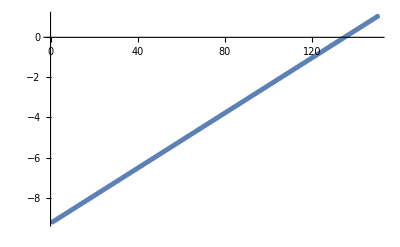

```mathematica
csol=Table[Log[Cons[i]],{i,1,T}]/.sol[[2]]; ListPlot[csol]
```

## Lessons

In optimization problems, make sure that the additive terms are of comparable magnitude.
When solving constrained optimization problems, make the constraints as linear as possible. Make the equations linear via transformations, or p.08.08.08ut nonlinearity in objective function